# Discrete Power-law fitter

```mathematica
Needs["ProgressMapping`",FileNameJoin[{NotebookDirectory[],"ProgressMapping.wl"}]]
```

```mathematica
DiscretePowerLawDistributionPDF[α_,xMin_,x_]:=x^-α/HurwitzZeta[α,xMin];
DiscretePowerLawDistributionCDF[α_,xMin_,x_]:=HurwitzZeta[α,x]/HurwitzZeta[α,xMin];
EmpiricalCDF[data_,x_]:= N[1-CDF[EmpiricalDistribution[data],x-1]];
GeneratePowerlawSampleData[α_,xMin_,xMax_,sampleSize_ :1000]:=Block[{dist},
dist = ProbabilityDistribution[DiscretePowerLawDistributionPDF[α,xMin,x],{x,xMin,xMax,1}];

RandomVariate[dist,sampleSize]

];
```

```mathematica
HistogramPoints[data_]:=Map[{#,N[Count[data,#]/Length[data]]}&,Sort[DeleteDuplicates[data]]];
HistogramPointPlots[data_List,opts: OptionsPattern[]]:=Block[{pltData = HistogramPoints[data]},
ListPlot[
pltData,
Joined->False,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{PointSize[Large],ColorData["Legacy"]["IndianRed"]},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FilterRules[{opts},Options[ListPlot]]
]
];
```

```mathematica
SelectTail[data_,xMin_]:=Select[data,#>=xMin&];
SelectBulk[data_,xMin_]:=Select[data,#<xMin&];
Estimateα[data_,xMin_]:=Block[{n,tail,α},
tail = SelectTail[data,xMin];
n = Length[tail];
α = N[1 + n (∑_(i=1)^n Log[tail[[i]]/(xMin-1/2)])^-1];
<|"Alpha"->α, "xMin"->xMin|>
];
EstimateαPrecise[data_,xMin_]:=Block[{tail,L},
tail = SelectTail[data,xMin];
L = Table[{α,CalculateLogLikelihood[tail,α, xMin]},{α,1.5,3.51,0.01}];
<|"Alpha"->MaximalBy[L,Last][[1,1]], "xMin"->xMin|>
];
```

```mathematica
KSStatistic[data_,xMin_Integer]:=Block[{xMax,tail,αEstimator,diff},
tail = SelectTail[data,xMin];
αEstimator = EstimateαPrecise[data,xMin]["Alpha"];
xMax = Max[data];
diff = Table[Abs[EmpiricalCDF[tail,x]-DiscretePowerLawDistributionCDF[αEstimator,xMin,x]],{x,xMin,xMax}];
Max[diff]
];
KSStatistic[data_,model_Association]:=Block[{xMax,tail,αEstimator,diff},
tail = SelectTail[data,model["xMin"]];
αEstimator = model["Alpha"];
xMax = Max[data];
diff = Table[Abs[EmpiricalCDF[tail,x]-DiscretePowerLawDistributionCDF[αEstimator,model["xMin"],x]],{x,model["xMin"],xMax}];
Max[diff]
];
KSStatistic[data_]:=KSStatistic[data,EstimateαAndXMin[data]];
CalculateLogLikelihood[data_,alpha_, xMin_]:=Block[{tail,n},
tail = SelectTail[data,xMin];
n = Length[tail];
N[- n * Log[HurwitzZeta[alpha,xMin]]-alpha ∑_(i=1)^n Log[tail[[i]]]]
];
EstimateαAndXMin[data_]:=Block[{minElement,maxElement,xMin},
{minElement,maxElement} = MinMax[data];
xMin = MinimalBy[Table[{x,KSStatistic[data,x]},{x,minElement,maxElement-1}],Last][[1,1]];
EstimateαPrecise[data,xMin]
];
GenerateBootstrapReplica[data_,model_]:=Block[{n,bulk, tail,tailProbability,tailReplica,bulkReplica},
n = Length[data];
bulk = SelectBulk[data,model["xMin"]];
tail = SelectTail[data,model["xMin"]];
tailProbability = 1.0 - Length[bulk]/n;
tailReplica = GeneratePowerlawSampleData[model["Alpha"],model["xMin"],Max[data],Floor[n*tailProbability]];
bulkReplica = RandomSample[bulk,n-Floor[n*tailProbability]];
RandomSample[Join[tailReplica, bulkReplica]]
];
GenerateFixedMinBootstrapReplica[model_,xMax_,n_]:=GeneratePowerlawSampleData[model["Alpha"],model["xMin"],xMax,n];
CalculateGOF[data_,replicas_:2000]:=Block[{model,ksOfData,syntheticKsValues,pValue},
model = EstimateαAndXMin[data];
ksOfData = KSStatistic[data,model];
syntheticKsValues = ProgressTable[KSStatistic[GenerateBootstrapReplica[data,model]],replicas];
pValue = N[Count[syntheticKsValues,x_ /; x>ksOfData]/Length[syntheticKsValues]];
<|"Alpha"->model["Alpha"],"xMin"->model["xMin"],"p-value"->pValue|>
];
CalculateFixedMinGOF[data_,xMin_,replicas_:2000]:=Block[{fixedMinModel,ksOfData,n,syntheticKsValues,pValue},
fixedMinModel = EstimateαPrecise[data,xMin];
ksOfData = KSStatistic[data,xMin];
n = Length[SelectTail[data,xMin]];
syntheticKsValues = ProgressTable[KSStatistic[GenerateFixedMinBootstrapReplica[fixedMinModel,Max[data],n]],replicas];
pValue = N[Count[syntheticKsValues,x_ /; x>ksOfData]/Length[syntheticKsValues]];
<|"Alpha"->fixedMinModel["Alpha"],"xMin"->fixedMinModel["xMin"],"p-value"->pValue|>
];
```

```mathematica
sample = GeneratePowerlawSampleData[2.5,1,100,2000];
```

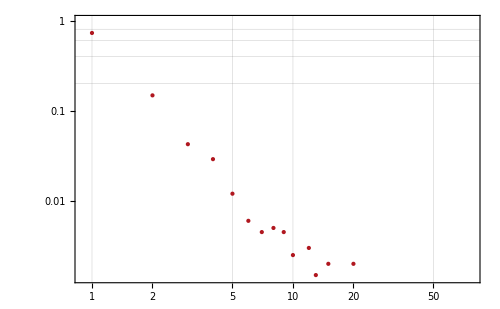

```mathematica
HistogramPointPlots[sample,
ScalingFunctions->{"Log","Log"},
PlotRange->{{0.9,Max[sample]+1},{0,1}}
]
```

Fixed x_min

```mathematica
fixedMinModel = Estimateα[sample,4]
```

<|Alpha→2.45174,xMin→4|>

```mathematica
CalculateFixedMinGOF[sample,4,2000]
```

<|Alpha→2.68281,xMin→4,p-value→0.0075|>

```mathematica
KSStatistic[sample,4]
```

0.5

Variable x_min

```mathematica
model = EstimateαAndXMin[sample]
```

<|Alpha→2.45,xMin→1|>

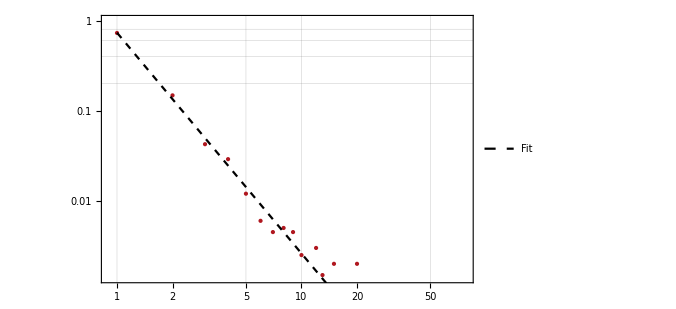

```mathematica
Show[
HistogramPointPlots[sample,
ScalingFunctions->{"Log","Log"},
PlotRange->{{0.9,Max[sample]+1},{0,1}}
],
Plot[DiscretePowerLawDistributionPDF[model["Alpha"],model["xMin"],x],{x,1,100},
ScalingFunctions->{"Log","Log"},
PlotLegends->{"Fit"},
PlotStyle->{Dashed,Black}
]
]
```

```mathematica
ksOfSample = KSStatistic[sample,model]
```

0.00846968

```mathematica
KSStatistic[GenerateBootstrapReplica[sample,model]]
```

0.0203975

```mathematica
ksValues = ProgressTable[KSStatistic[GenerateBootstrapReplica[sample,model]],1000];
```

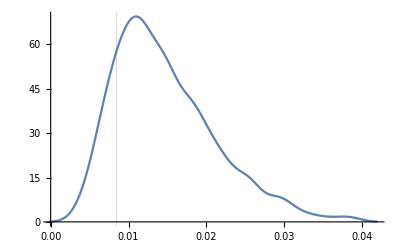

```mathematica
SmoothHistogram[ksValues,GridLines->{{ksOfSample},{}}]
```

```mathematica
N[Count[ksValues,x_ /; x>ksOfSample]/Length[ksValues]]
```

0.85

```mathematica
CalculateGOF[sample]
```

<|Alpha→2.08014,xMin→4,p-value→0.8395|>